### Parameter definitions

```mathematica
FullSimplify[1/(2 d^3)((4+3q)L[t]-(3q M^2 ξ)/(q+1) L[t]/Norm[L[t]]  + S2[t]   )   /.ξ->M^-2 Dot[((1+q)S1[t]+(1+q^-1)S2[t]),L[t]/Norm[L[t]]]/.L[t] ->J[t]-S1[t]-S2[t]]
FullSimplify[1/(2 d^3)((4+3/q)L[t]-(3 M^2 ξ)/(q+1) L[t]/Norm[L[t]]  + S1[t]    )    /.ξ->M^-2 Dot[((1+q)S1[t]+(1+q^-1)S2[t]),L[t]/Norm[L[t]]]/.L[t] ->J[t]-S1[t]-S2[t]]
```

((4+3 q) (J[t]-S1[t]-S2[t])+S2[t]+(3 q ((1+q) (q S1[t]+S2[t]))/q.(-(-J[t]+S1[t]+S2[t])/Norm[J[t]-S1[t]-S2[t]]) (-J[t]+S1[t]+S2[t]))/((1+q) Norm[J[t]-S1[t]-S2[t]]))/(2 d^3)

(S1[t]+(4+3/q) (J[t]-S1[t]-S2[t])+(3 ((1+q) (q S1[t]+S2[t]))/q.(-(-J[t]+S1[t]+S2[t])/Norm[J[t]-S1[t]-S2[t]]) (-J[t]+S1[t]+S2[t]))/((1+q) Norm[J[t]-S1[t]-S2[t]]))/(2 d^3)

```mathematica
d=1;
(*Use xi. Don't specify arbitrarity. Replace xi with L, S1, S2 vectors in NDSolve.

Think about how to take care of NDSolve.

Perform xcaptest. Should be constant
*)
q=0.6;
```

### Differential equations

```mathematica
dS1[t_] =   Cross[1/(2 d^3)((4+3q)(J[t]-S1[t]-S2[t])-(3q)/(q+1)((1+q)Dot[S1[t],J[t]-S1[t]-S2[t]]+(1+1/q)Dot[S2[t],J[t]-S1[t]-S2[t]]) (J[t]-S1[t]-S2[t])/Norm[J[t]-S1[t]-S2[t]]^2  + S2[t]   )  ,S1[t]];
dS2[t_] =    Cross[1/(2 d^3)((4+3/q)(J[t]-S1[t]-S2[t])-3/(q+1)((1+q)Dot[S1[t],J[t]-S1[t]-S2[t]]+(1+1/q)Dot[S2[t],J[t]-S1[t]-S2[t]]) (J[t]-S1[t]-S2[t])/Norm[J[t]-S1[t]-S2[t]]^2    + S1[t]    ) ,S2[t]];
dJ[t_]=     {0,0,0}  ;
```

### Numerical solution

```mathematica
S10={-3,-6,-1};
S20={-4,-6,-3};
J0={0,0,12};
```

```mathematica
sol=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , J'[t]==dJ[t],S1[0]==S10,S2[0]==S20, J[0]==J0   },   {S1,S2,J},{t,0,30}];
```

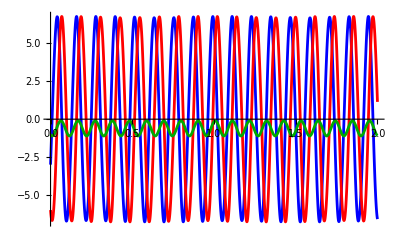

```mathematica
output[t_]:= (S1/.sol[[1]])[t];
Plot[{output[t][[1]],output[t][[2]],output[t][[3]]}, {t,0,2},PlotStyle->{Blue,Red,Darker[Green]}]
```

#### Vector definitions with numerical solution

```mathematica
S1v[t_]:=(S1/.sol[[1]])[t];
S2v[t_]:=(S2/.sol[[1]])[t];
Jv[t_]:=(J/.sol[[1]])[t];
Lv[t_]:=Jv[t]-S1v[t]-S2v[t];
Sv[t_]:=S1v[t]+S2v[t];
```

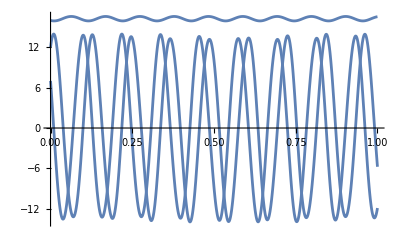

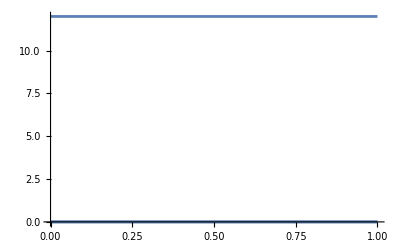

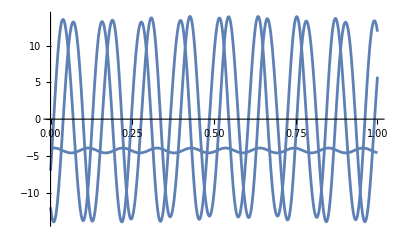

```mathematica
Plot[Lv[t],{t,0,1}]
Plot[Jv[t],{t,0,1}]
Plot[Sv[t],{t,0,1}]
```

#### Vector modulus

```mathematica
NormS1[t_]:=Norm[S1v[t]];
NormS2[t_]:=Norm[S2v[t]];
NormJ[t_]:=Norm[Jv[t]];
NormL[t_]:=Norm[Lv[t]];
NormS[t_]:=Norm[Sv[t]];
```

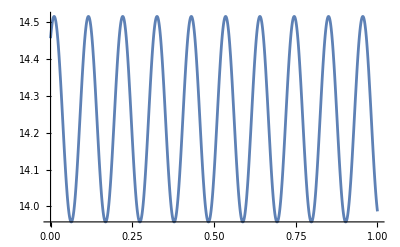

```mathematica
Plot[NormS[t],{t,0,1}]
```

#### Unit vector definitions

```mathematica
S1u[t_]:=S1v[t]/NormS1[t];
Su[t_]:=Sv[t]/NormS[t];
```

#### Cartesian unit vectors test

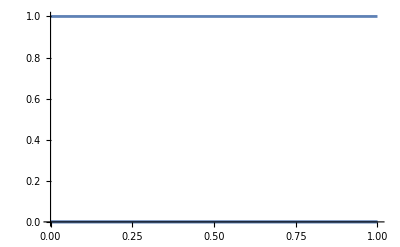

```mathematica
zcapZ[t_]:=Jv[t]/(Jv[t][[3]])
Plot[zcapZ[t],{t,0,1}]
```

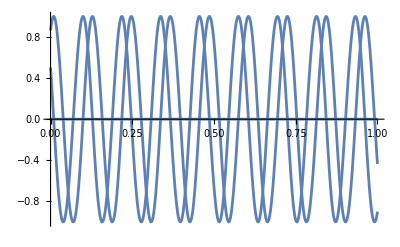

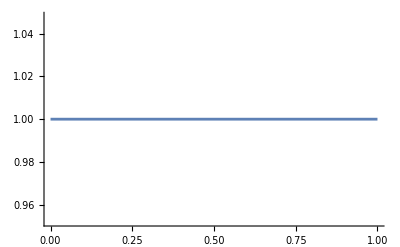

```mathematica
xcapX[t_]:=(Lv[t]-(Dot[Lv[t],zcapZ[t]]zcapZ[t]))/Norm[Lv[t]-(Dot[Lv[t],zcapZ[t]]zcapZ[t])]
Plot[xcapX[t],{t,0,1}]
Plot[Norm[xcapX[t]],{t,0,1}]
```

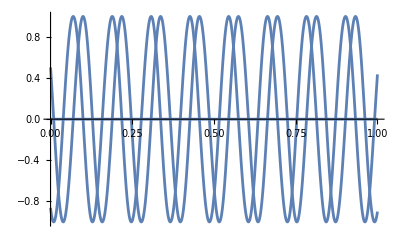

-Graphics-

```mathematica
ycapY[t_]:=Cross[zcapZ[t],xcapX[t]]
Plot[ycapY[t],{t,0,1}]
Plot[Norm[ycapY[t]],{t,0,1}]
```

#### Orthogonal vector definition

```mathematica
SO1[t_]:=Cross[ycapY[t],Sv[t]];
NormSO[t_]:=Norm[SO1[t]];
SOu[t_]:=SO1[t]/NormSO[t]
```

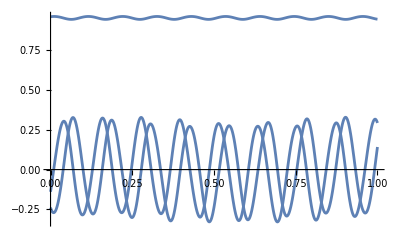

```mathematica
Plot[SOu[t],{t,0,1},PlotRange->All]
```

#### Angle ϕ' definitions

```mathematica
cosϕ1[t_]:=Dot[S1u[t],SOu[t]]/Norm[Cross[S1u[t],Su[t]]];
```

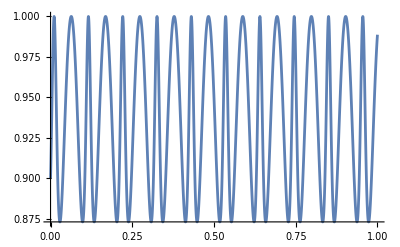

```mathematica
Plot[cosϕ1[t],{t,0,1},PlotRange->All]
```

#### Effective potential ξ (constant of motion) evolution

```mathematica
ξ01[t_]:=Dot[((1+q)S1v[t]+(1+q^-1)S2v[t]),Lv[t]/NormL[t]]
ξ02[t_]:=1/(4 q NormL[t] NormS[t]^2)((-1+q^2) cosϕ1[t] √(NormJ[t]^2-(NormL[t]-NormS[t])^2) √(-NormJ[t]^2+(NormL[t]+NormS[t])^2) √(NormS[t]^2-(NormS1[t]-NormS2[t])^2) √(-NormS[t]^2+(NormS1[t]+NormS2[t])^2)+(NormJ[t]^2-NormL[t]^2-NormS[t]^2) ((1+q)^2 NormS[t]^2+(-1+q^2) (NormS1[t]^2-NormS2[t]^2)))
```

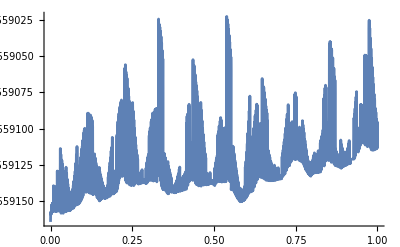

-Graphics-

```mathematica
Plot[ξ01[t],{t,0,1},PlotRange->All]
Plot[ξ02[t],{t,0,1},PlotRange->All]
```

### Test for initial conditions

#### Initial conditions

```mathematica
nS10=N[Norm[S10]];
nS20=N[Norm[S20]];
nJ0=N[Norm[J0] ];
nL0=N[Norm[J0-S10-S20]];
nSv0=N[Norm[S10+S20]]
rules0={J->nJ0,L->nL0,S1->nS10,S2->nS20};
```

14.4568

```mathematica
J>S1+S2-L//.rules0
```

True

```mathematica
Smin0=Max[Abs[J-L],Abs[S1-S2]]//.rules0
Smax0=Min[J+L,S1+S2]//.rules0
```

9.18962

14.5926

```mathematica
S1+S2-L//.rules0
{L-Abs[S1-S2],S1+S2-L}//.rules0
```

-6.59704

{20.1617,-6.59704}

```mathematica
ξmax0=1/(4 L  q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.rules0/.S->Smin0
ξmin0=1/(4 L  q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.rules0/.S->Smax0
```

-20.4751

-26.532

```mathematica
ContξSp=1/(4 L  q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.rules0/.Cos[ϕ]->-1//FullSimplify;
ContξSm=1/(4 L  q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])//.rules0/.Cos[ϕ]->+1//FullSimplify;
```

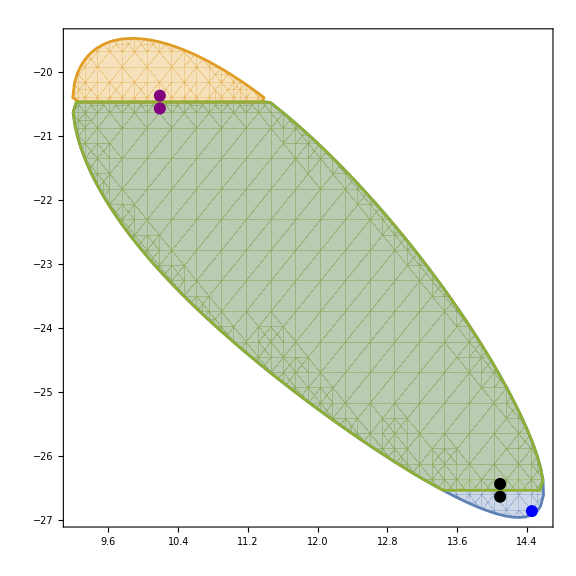

```mathematica
Show[RegionPlot[{ξ>ContξSm&&ξ<ContξSp&&ξ<ξmax0,ξ>ContξSm&&ξ<ContξSp&&ξ>ξmax0,ξ>ContξSm&&ξ<ContξSp&&ξmin0<ξ<ξmax0},{S,Smin0,Smax0},{ξ,ξmin0-1.5,ξmax0+1.5},PlotRange->{All,All},ImageSize->Large],Graphics[{PointSize[0.015],Blue,Point[{nSv0,ξ01[0]}]}],Graphics[{PointSize[0.015],Black,Point[{Smax0-0.5,ξmin0-0.1}]}],Graphics[{PointSize[0.015],Black,Point[{Smax0-0.5,ξmin0+0.1}]}],Graphics[{PointSize[0.015],Purple,Point[{Smin0+1,ξmax0+0.1}]}],Graphics[{PointSize[0.015],Purple,Point[{Smin0+1,ξmax0-0.1}]}]]
```

```mathematica
ξ01[0]
```

-26.8559

```mathematica
Clear[ξ]
```

```mathematica
UpperBound={S->Smin0+1,ξ->ξmax0+0.1}
```

{S→10.1896,ξ→-20.3751}

{S→10.1896,ξ→-20.3751}

### Numerical test new initial conditions

```mathematica
S11={-3.0346177564371164,-6.05934472532072,-1.0197815751069141};
S21={-4.034617756437072,-6.05934472532072,-3.0197815751069363};
J1=J0;
L1=J1-S11-S21;
Sv1=S11+S21
```

{-7.06924,-12.1187,-4.03956}

```mathematica
nS11=N[Norm[S11]];
nS21=N[Norm[S21]];
nJ1=N[Norm[J1] ];
nL1=N[Norm[J1-S11-S21]];
nSv1=N[Norm[S11+S21]]
rules1={J->nJ1,L->nL1,S1->nS11,S2->nS21};
```

14.5998

```mathematica
nJ1>nS11+nS21-nL1
```

True

```mathematica
Smin1=Max[Abs[nJ1-nL1],Abs[nS11-nS21]]
Smax1=Min[nJ1+nL1,nS11+nS21]
```

9.30972

14.7342

```mathematica
Dot[((1+q)S1+(1+q^-1)S2),L/Norm[L]]/.{S1->S11,S2->S21,L->L1} (*constant of motion ξ*)
```

-27.1717